```mathematica
Sum[(n^j)*(pq-j-1),{j,0,pq-2}]
```

9+8 n+7 n^2+6 n^3+5 n^4+4 n^5+3 n^6+2 n^7+n^8

```mathematica
Sum[(n^j)*(pq-j-1),{j,0,pq-3}]
```

9+8 n+7 n^2+6 n^3+5 n^4+4 n^5+3 n^6+2 n^7

```mathematica
FullSimplify[-(n^2+n^pq-2 n^(1+pq)-n^2 pq+n^3 pq)/((-1+n)^2 n^2)]
```

9+n (8+n (7+n (6+n (5+n (4+n (3+2 n))))))

```mathematica
pq:= 10
```

```mathematica
f42[n_]:= Sum[(n^j)*(pq-j-1),{j,0,pq-2}]
```

```mathematica
Print[{f42[Range[2,8]]}]
```

{{1013,14757,116505,610349,2418645,7846533,21913097}}

```mathematica
Sum[(a^j)*(w - j - 1),{j,0,w-2}]
```

-(1-a^w-w+a w)/(-1+a)^2

```mathematica
Plot3D[-(1-a^w-w+a w)/(-1+a)^2,{a,2,6.},{w,2,10}]
```

-Graphics3D-

```mathematica
s2[a_,w_]:= ((1-a^w)/(1-w))+Sum[(a^j)*(w - j - 1),{j,0,w-2}]
```

```mathematica
s1[a_,w_]:=Binomial[a,a/2]*(1-a^w)/(1-w)
```

```mathematica
Print[{s1[Range[2,8],10]}]
```

{{682/3,1889536/(27 π),699050,1666666496/(45 π),1209323500/9,385672871936/(105 π),8351325290}}

```mathematica
Print[{s2[Range[2,8],10]}]
```

{{3380/3,191861/9,699040/3,5086255/3,82233980/9,117698015/3,141217744}}

```mathematica
Sum[j*(z^j),{j,0,u}]
```

(z+z^(1+u) (-1-u+u z))/(1-z)^2

```mathematica
Sum[(a^j)*(-1+2z-2j),{j,0,z-3}]
```

-(a^2+a^3+3 a^z-5 a^(1+z)-2 a^2 z+2 a^3 z)/((-1+a)^2 a^2)

```mathematica
Simplify[Out[31]]
```

-(3 a^z-5 a^(1+z)+a^2 (1-2 z)+a^3 (1+2 z))/((-1+a)^2 a^2)

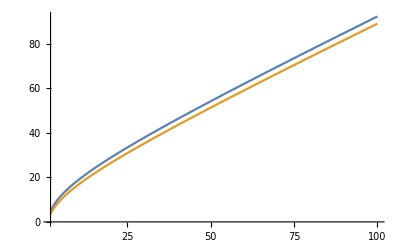

```mathematica
Plot[{Log[(2^n)*n^5],Log[(2^n/Sqrt[2Pi*n])*n^5]},{n,2,100}]
```

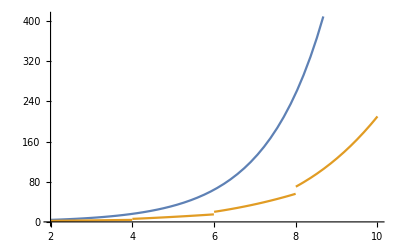

```mathematica
Plot[{2^n,Binomial[n,Floor[n/2]]},{n,2,10}]
```

```mathematica
faux[n_]:=Binomial[n,Floor[n/2]]
```

```mathematica
ListPlot[{Labeled[2^Range[2,10],2^n ],Labeled[faux[Range[2,10]],Binomial[n,Floor[n/2]]]}]
```

-Graphics-

```mathematica
Export["/Users/jp/Documents/curvecomparison.pdf",%14,"PDF"]
```

/Users/jp/Documents/curvecomparison.pdf